# QBMMlib: Examples

## Clear variables , load package, read documentation

```mathematica
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlib.wl"];
?QBMMlib`*
```

## Select example and inversion method

```mathematica
(* Options: Linear1D, Linear2D, Nonlinear2D *)
case="Nonlinear2D";

(* 1D Options: "AQMOM", "QMOM", "HYQMOM", *)
(* 2D Options: "CQMOM", "CHYQMOM"*)
method="CHYQMOM" ;
```

## Initialize and simulate

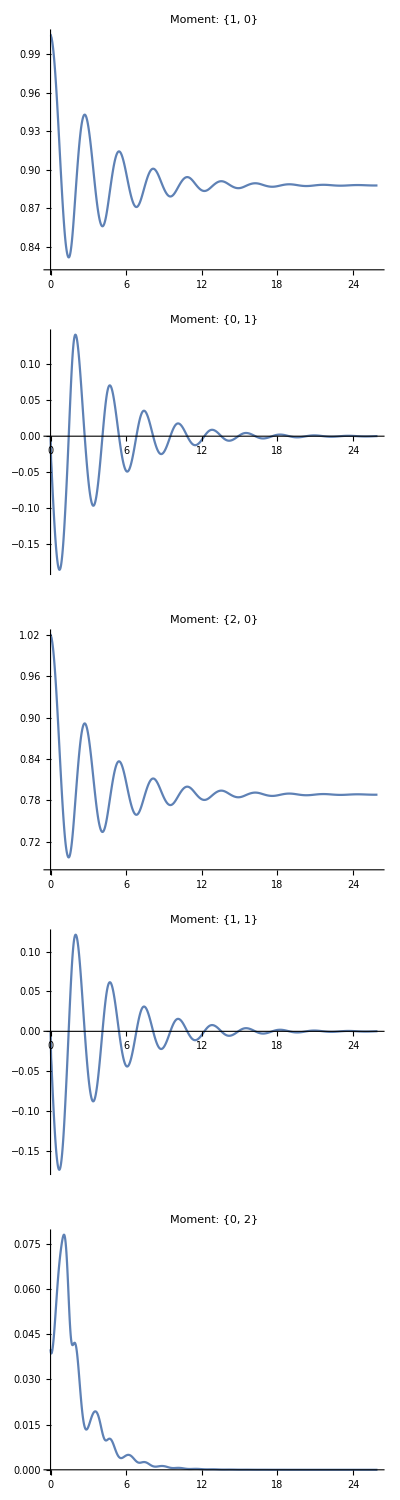

```mathematica
If[case=="Linear1D",
	eqn=x'[t]==4x[t]-2 x[t]^2;
	depvar=x[t];
	indvar=t;
	
	T=2;
	
	n={3};
	μ1=0.5;σ1=0.1;
	NDF=NormalDistribution[μ1,σ1];
];
If[case=="Linear2D",
	eqn=x''[t]+x'[t]+x[t]==0;
	depvar=x[t];
	indvar=t;
	
	T=15;

	n={2,2};
	μ1=1.;σ1=0.1;
	P1=LogNormalDistribution[Log[μ1],σ1];
	μ2=0;σ2=0.2;
	P2=NormalDistribution[μ2,σ2];		
	NDF=ProductDistribution[P1,P2];
];
If[case=="Nonlinear2D",
	Cp=10/7;
	Rey=10;
	eqn=r[t] r''[t]+3/2 r'[t]^2+4/Rey r'[t]/r[t]==(1/r[t])^3-Cp;
	depvar=r[t];
	indvar=t;
	
	Toneperiod=3.4(1/Cp)^(3/4);
	Nperiod=10;
	T=Nperiod Toneperiod;
	
	n={2,2};
	μ1=1.;σ1=0.1;
	P1=LogNormalDistribution[Log[μ1],σ1];
	μ2=0;σ2=0.2;
	P2=NormalDistribution[μ2,σ2];
	NDF=ProductDistribution[P1,P2];
];

(* Get moment transport equations *)
{coefs,exps}=TransportTerms[eqn,depvar,indvar];

(* Set permutations, compute moment set indices *)
perms=If[method=="CQMOM",{12,21},{12}];
nperm=Length[perms];
momidx=MomentIndex[n,method,nperm];

(* Compute RHS function [only required for nperm > 1] *)
RHS[moms_,myt_]:=Module[{rhs,mom,mout,rout,w,xi},
	Do[
		{w,xi}=MomentInvert[moms,momidx,Method->method,Permutation->perms[[i]]];
		rhs[i]=ComputeRHS[w,xi,momidx,{coefs,exps}];
		mom[i]=Project[w,xi,momidx];
	,{i,nperm}];
	mout=Sum[mom[i],{i,nperm}]/nperm;
	rout=Sum[rhs[i],{i,nperm}]/nperm;
	Return[{mout,rout},Module];
];

(* Adaptive SSP-RK2/3 time integration parameters *)
dt0=dt=10^-5;
dtmax=10^4 dt;
etol=10^-5;

(* Set initial conditions and simulate *)
GenMoment[idx_]:=If[Length[RandomVariate[NDF]]>1,Moment[NDF,idx],Moment[NDF,idx[[1]]]];
moms=Map[GenMoment,momidx];

sol={};time=0;dt=dt0;
Monitor[While[time≤T,
	{moms,e}=RK23[moms,RHS,time,dt];
	AppendTo[sol,{time,moms}];

	time=time+dt;
	dt=dt Min[Max[Sqrt[etol/(2 e)],0.3],2];
dt=Min[Max[0.9 dt,dt0],dtmax];

If[Norm[moms]>10^5,Print["Crash ",100 time/T];Break[]];
	If[e<10^-16&&time>0.1T,Print["Error zero, stationary point reached. Aborting."];Break[]];
];
,Row[{"% Completed: "<>ToString[NumberForm[100time/T,{3,2}]]}]
];

TableForm[Table[ListPlot[Thread[{sol[[All,1]],Flatten[sol[[All,2,i]]]}],Joined->True,PlotRange->All,PlotLabel->"Moment: "<>ToString[momidx[[i]]]],{i,2,Length[momidx]}]]
```